```mathematica
ClearAll["Global`*"]
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

## Importar datos

```mathematica
dataPath=FileNameJoin[{NotebookDirectory[],"data"}];
dataFiles=FileNames["*.csv",dataPath]
```

{/Users/horacio/Desktop/RETODCI4/data/BOLSA EN ROLLO.csv,/Users/horacio/Desktop/RETODCI4/data/EXTRUSION.csv,/Users/horacio/Desktop/RETODCI4/data/IMPRESION.csv,/Users/horacio/Desktop/RETODCI4/data/SELLADO.csv}

### Genera BD de EXTRUSION

```mathematica
Clear[extrusion,EData]
extrusion=Import[dataFiles[[2]],"Data",CharacterEncoding->"UTF8"];(*extrusion*)
EData[]=extrusion[[1]];
MapThread[Set,{EData/@EData[],N[Transpose[extrusion[[2;;]]]]}];
```

```mathematica
EData[]
```

{SEMANA,FECHA,TURNO,EXTRUSORA,OPERADOR,N° DE PEDIDO,NOMBRE DE PEDIDO,CLAVE SAP,TIPO DE PRODUCTO,MEDIDA DE LA BOLSA,TRATADO,ANCHO DE PELICULA,N° DE ROLLO,CALIBRE PEDIDO,CALIBRE REAL,MOTIVO DEL CORTE,HORA INICIO,HORA FINAL,KILOS/HORA,PRODUCTO CONFORME,% DE PRODUCTO CONFORME,RECUP.,% DE RECUP,BASURA,% DE BASURA,CONSUMO MP,% MATERIA PRIMA,REC.AREA ROLLO,REC.AREA SELLADO,RECUPERADO DEVOLUCION ROLLO,HORAS DE TRABAJO,,,,,,,,,,,,,,,,,,}

### Genera BD de IMPRESION

```mathematica
Clear[impresion,IData]
impresion=Import[dataFiles[[3]],"Data",CharacterEncoding->"UTF8"];(*sellado*)
IData[]=impresion[[1]];
MapThread[Set,{IData/@IData[],N[Transpose[impresion[[2;;]]]]}];
```

```mathematica
IData[]
```

{SEMANA,FECHA,TURNO,IMPRESORA,OPERADOR,N° DE PEDIDO,CLAVE SAP,NOMBRE DE PEDIDO,TIPO DE PRODUCTO,ANCHO DE PELICULA,TINTAS,FOLIO DEL ROLLO,HORA INICIO,HORA FINAL,PESO DE ROLLO,RECUPERADO,% DE RECUP,HORAS DE TRABAJO,DISCO,Columna1,Columna2,Columna3,Columna4,Columna5,Columna6}

### Genera BD de SELLADO

```mathematica
Clear[sellado,SData]
sellado=Import[dataFiles[[4]],"Data",CharacterEncoding->"UTF8"];(*sellado*)
SData[]=sellado[[1]];
MapThread[Set,{SData/@SData[],N[Transpose[sellado[[2;;]]]]}];
```

```mathematica
SData[]
```

{FECHA,SEMANA,TURNO,HORA DE INICIO,RESPONSABLE,OPERADORES,NUMERO DE PEDIDO,SELL.,NOMBRE DEL PEDIDO,TIPO DE BOLSA,MEDIDA,CALIBRE,GPM (Golpes por minuto),TEMPERATURA DE SELLADO (INFERIOR),TEMPERATURA DE SELLADO (SUPERIOR),PESO/BULTO,KG/DE BOBINA,N° DE BULTOS,PROMEDIO,MILLARES,SERIALIZADO INICIO,SERIALIZADO FIN,PESO DE TROQUEL,MERMA EXTRUSION,CAUSAS EXTRUSION,MER IMPRESIÓN,CAUSAS IMPRESIÓN,IMPRESIÓN  MERMA POR PROCESO,MERMA SELLADO,CAUSAS SELLADO,BOLSA DE 2A,ORIGEN,CUARENTENA,BASURA,MUESTRAS,HORA FINAL,HORAS DE TRABAJO}

```mathematica
NotebookDirectory[]
```

/Users/horacio/Desktop/RETODCI4/

```mathematica
NotebookOpen[FileNameJoin[{NotebookDirectory[],"BasicClean.nb"}]]
```

pt97r_shm41FrontEndObject[LinkObject["pt97r_shm", 3, 1]]41BasicClean.nb/Users/horacio/Desktop/RETODCI4/BasicClean.nb

### Genera subBD de merma registrada al final del proceso de sellado

```mathematica
mermasPos=Position[Boole@StringMatchQ[SData[],"*MERMA*"],1]
mermasLab=Extract[k$ds,%]
```

{FECHA,SEMANA,TURNO,HORA DE INICIO,RESPONSABLE,OPERADORES,NUMERO DE PEDIDO,SELL.,NOMBRE DEL PEDIDO,TIPO DE BOLSA,MEDIDA,CALIBRE,GPM (Golpes por minuto),TEMPERATURA DE SELLADO (INFERIOR),TEMPERATURA DE SELLADO (SUPERIOR),PESO/BULTO,KG/DE BOBINA,N° DE BULTOS,PROMEDIO,MILLARES,SERIALIZADO INICIO,SERIALIZADO FIN,PESO DE TROQUEL,MERMA EXTRUSION,CAUSAS EXTRUSION,MER IMPRESIÓN,CAUSAS IMPRESIÓN,IMPRESIÓN  MERMA POR PROCESO,MERMA SELLADO,CAUSAS SELLADO,BOLSA DE 2A,ORIGEN,CUARENTENA,BASURA,MUESTRAS,HORA FINAL,HORAS DE TRABAJO}

{{24},{28},{29}}

{MERMA EXTRUSION,IMPRESIÓN  MERMA POR PROCESO,MERMA SELLADO}

```mathematica
SData[]=ds[[1]];
```

```mathematica
MapThread[Set,{SData/@SData[],N[Transpose[ds[[2;;]]]]}];
```

```mathematica
(*Row[
ListPlot[SData[#],PlotLabel->#,ImageSize->170]&/@SData[]
]*)
```

$Aborted

#### Veamos como estan distribuidas las fechas

Es claro que tenemos que ordenarlos de alguna manera. Veamos por ejemplo como ordenarlos por fecha para crear eventos

Nota: Se sugiere que la base de captura compare la fecha de captura con la fecha actual del sistema para evitar errores como el encontrado en las fechas de SELLADO.

```mathematica
fechas=DeleteMissing[ds[[2;;,1]]/.""->Missing[],∞];
fechas=DateObject[{#,{"Day","Month","Year"}},"Day"]&/@fechas;
```

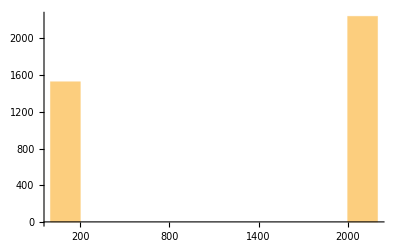

```mathematica
DateHistogram[fechas]
```

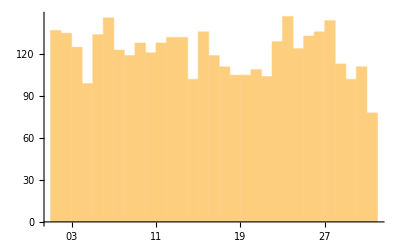

```mathematica
DateHistogram[fechas,"Days",DateReduction->"Month"]
```

```mathematica
DateHistogram[fechas,"Days",DateReduction->"Week"]
```

$Aborted

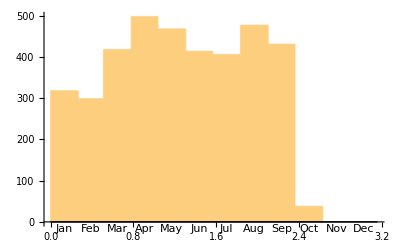

```mathematica
DateHistogram[fechas,"Month",DateReduction->"Year"]
```

#### Está registrada la merma por cada proceso asi que veamos como se distribuye de acuerdo a cada uno

Extrae los valores de la base de datos donde la merma por extrusion es mayor que cero

```mathematica
MermaExtrusion[]=ds[[1]];
```

No me acuerdo que es pme asi que mejor no evalues la celda siguiente, lo cual es un pedo poruqe...no se qeu es pme

```mathematica
pme=Position[SData["MERMA EXTRUSION"],_?(#≠0&)];
```

```mathematica
MapThread[Set,{MermaExtrusion/@MermaExtrusion[],Extract[SData[#],pme]&/@SData[]}]
Dimensions@%
```

{1}
 |  |  |  |

{37,811}

#### WordClouds

Visualiza causas de  merma

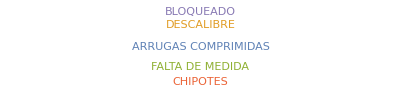

```mathematica
MermaExtrusion["CAUSAS EXTRUSION"]//WordCloud(*anonimizar*)
```

Visualiza los responsables que mas aparecen en merma positiva

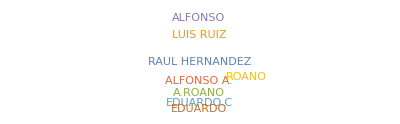

```mathematica
MermaExtrusion["RESPONSABLE"]//WordCloud(*anonimizar*)
```

Visualiza los operadores que mas aparecen en merma positiva

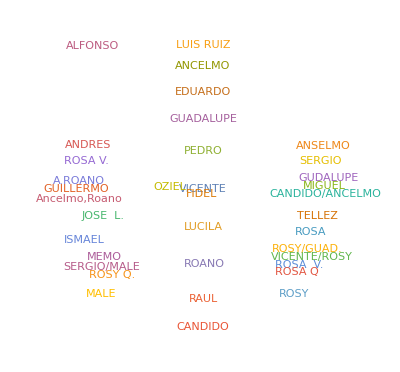

```mathematica
MermaExtrusion["OPERADORES"]//WordCloud(*anonimizar*)
```

Visualiza los tipos de bolsa con merma

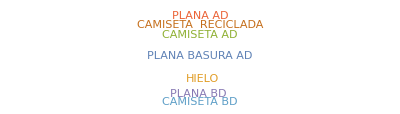

```mathematica
MermaExtrusion["TIPO DE BOLSA"]//WordCloud(*anonimizar*)
```

Visualiza medida y calibre con merma

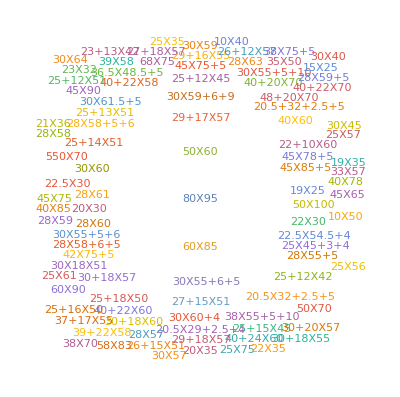

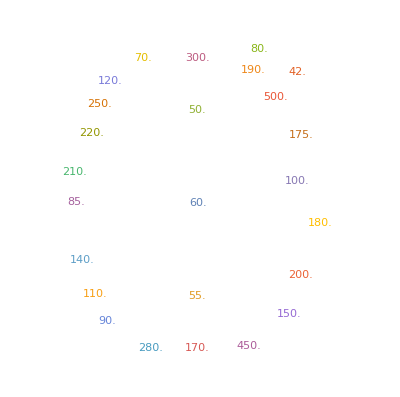

```mathematica
MermaExtrusion["MEDIDA"]//WordCloud
MermaExtrusion["CALIBRE"]//WordCloud
```

#### Frequency of events by type

Frecuencia de merma por sellado y por tipo de bolsa

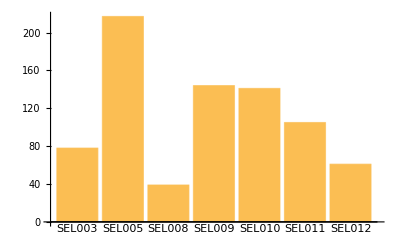

```mathematica
tallydata=SortBy[Tally[ToString/@MermaExtrusion["SELL."]],First];
BarChart[tallydata[[All,2]],ChartLabels->(tallydata[[All,1]])]
```

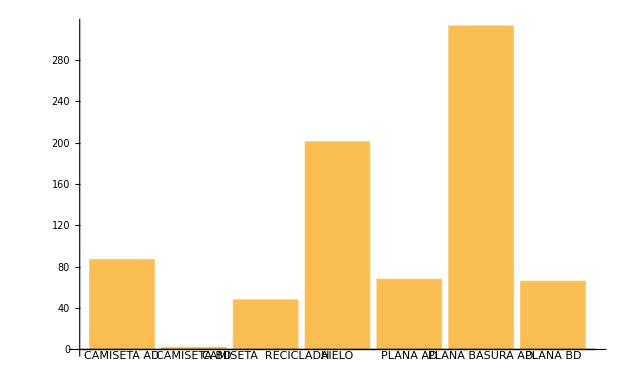

```mathematica
tallydata=SortBy[Tally[ToString/@MermaExtrusion["TIPO DE BOLSA"]],First];
BarChart[tallydata[[All,2]],ChartLabels->(tallydata[[All,1]])]
```

frecuencia de las horas de trabajo que se registraron con merma en extrusion

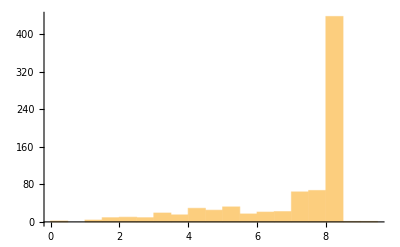

```mathematica
Histogram[MermaExtrusion["HORAS DE TRABAJO"]]
```

```mathematica
MinMax[MermaExtrusion["HORAS DE TRABAJO"]]
```

{0.,9.}

#### Merma por tipo de bolsa

```mathematica
GroupBy[Transpose[MermaExtrusion[#]&/@{"MERMA EXTRUSION","TIPO DE BOLSA"}],Last->First,Total]//Sort
ListPlot@%
```

<|CAMISETA BD→6.84,PLANA AD→209.27,CAMISETA AD→285.12,PLANA BD→292.28,CAMISETA  RECICLADA→538.16,PLANA BASURA AD→538.42,HIELO→679.76|>

-Graphics-

```mathematica
GroupBy[Transpose[MermaExtrusion[#]&/@{"MERMA EXTRUSION","SELL."}],Last->First,Total]//Sort
ListPlot@%
```

<|SEL008→85.81,SEL003→143.16,SEL012→181.5,SEL011→259.72,SEL005→410.11,SEL010→627.53,SEL009→842.02|>

-Graphics-

#### Distribucion de masa del producto que tiene merma por extrusion

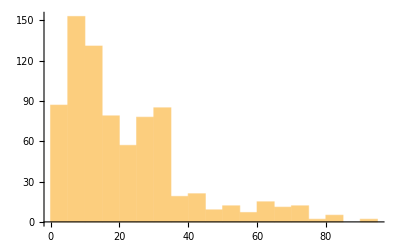

```mathematica
Histogram[MermaExtrusion["N° DE BULTOS"]]
```

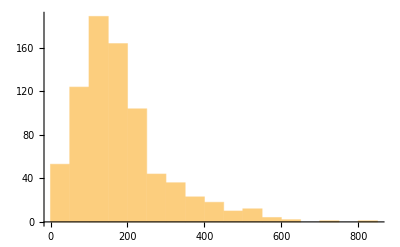

```mathematica
Histogram[MermaExtrusion["PESO/BULTO"]]
```

```mathematica
dist=FindDistribution[pesoBulto=MermaExtrusion["PESO/BULTO"]]
```

ExtremeValueDistribution[130.967,83.4206]

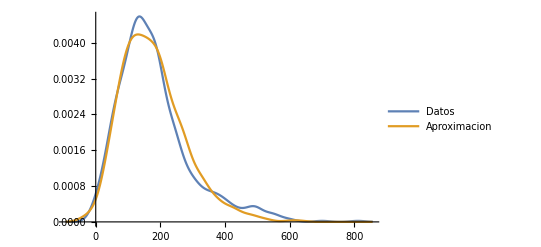

```mathematica
SmoothHistogram[{pesoBulto,RandomVariate[dist,Length[pesoBulto]]},PlotLegends->{"Datos","Aproximacion"}]
```

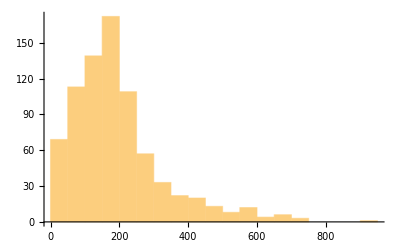

```mathematica
Histogram[pesoBovina=DeleteMissing[MermaExtrusion["KG/DE BOBINA"]/.""->Missing[]]]
```

```mathematica
dist=FindDistribution[pesoBovina]
```

FindDistribution::conenf: The data will be treated as continuous. Use the option TargetFunctions->Discrete otherwise.

MixtureDistribution[{0.805599,0.194401},{NormalDistribution[148.252,77.1908],NormalDistribution[374.039,173.235]}]

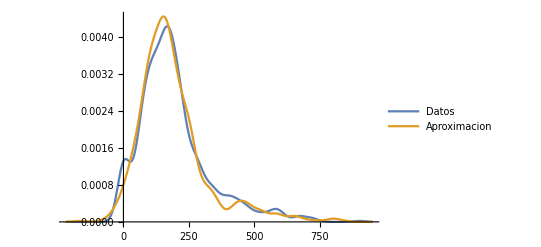

```mathematica
SmoothHistogram[{pesoBovina,RandomVariate[dist,Length[pesoBovina]]},PlotLegends->{"Datos","Aproximacion"}]
```

```mathematica
Show[
```

### El numero de pedido deberia relacionarse con la base de extrusion ... ...

```mathematica
MermaExtrusion/@{"NUMERO DE PEDIDO","NOMBRE DEL PEDIDO"};
Dimensions/@%
```

{{1},{1}}

```mathematica
claveMerma=First/@Tally[
MermaExtrusion["NOMBRE DEL PEDIDO"]
]
```

{ELL-001,BAMA-001,PROI-007,TEPU-003,CRIS-003,TEVE-003,FAUN-004,TEVE-005,FRES-002,POLE-001,FAUN-001,ELEC-002,PLUS-003,CHED-002,PANT-005,QHAC-004,SAVE-004,TOGA-001,SAVE-002,QCHI-010,CARA-001,CHED-001,VIPU-001,QCHI-006,TEPU-001,QCHI-003,ELLL-001,POFE-003,AMON-001,COME-004,COME-006,PROI-029,KEES-001,PROI-028,LARY-001,CHED-003,ARCU-003,HECL-003,TEPU-004,GOBI-002,HICO-002,SAPI-002,ROLL-002,TEPU-006,AMCO-002,FRES-001,MQEH-001,HIJU-001,BAMA-002,HDYP-002,PACI-003,TOGA-002,ZAVE-004,FUND-030,POPO-002,HDYP-003,FUND-031,HIIG-002,TEPU-008,PFLX-011,QCHI-005,QCHI-011,MRHI-002,X24-003,TIBU-002,MRHI-001,HIEL-003,HIBO-002,MRHI-003,HK-2-001,VIHU-002,CHEDE-001,BELLE-001,,CRIS-004,TEVE-001,MANA-006,CRES-003,PRIS-001,YUPI-001,DAUZ-003,CAST-003,CHED.003,CAST-005,IRIS-005,CAST-002,ALVA-001,IMCO-001,IRIS-006,MOLI-002,IMCO-002,SHIF-002,OFIX-004,CRYS-001,ZAVE-005,POPO-001,POSI-001,X24-006,HOSO-001,POFE-004,SALV-003,QHAC-005,ARGO-002,QHAC-009,IRIS-002,ARGO-003,IRIS-004,SALV-002,GAMM-001,HECL-004,SUPO-001,LUGA-003,ELNO-001,SOLE-001,OFIX-002,HITU-002,OFIX-003,X-24-003,FLHU-002,X-24-006,BOMA-001,BOMA-002,CRIS-002,FRES-003,CRIS-001,BRIZ-001,PROI-047,PROI-046,PROI-048,SUBO-001,CHED-03,CUEN-002,HECL-005,YOPZ-002,ZAVE-003,MIZU-001,ISSI-004,TEVE-002,FRES-004,ISSI-003,ALVA-002,VIPU-002,ROLL-001,ZASE-005,PPLO-001,LAMO-001,X24-004,PROI-29,ULTR-001,FUND-033,AGRN-001,COIN-003,EMPAQUE-001,IRIS-003,CHED-005,KEES-010,ZBAE-001,HECL-002,LAVI-002,PFLX-012,HIEL-002}

#### Cargamos la base de datos de extrusion

```mathematica
Transpose[de[[2;;]]]
```

{1}
 |  |  |  |

```mathematica
Clear[EData,de]
```

```mathematica
dataFiles[[2]]
```

/Users/horacio/Desktop/BASES DE DATOS/BITACORA EXTRUSION 2019.xlsx

```mathematica
de=Import[dataFiles[[2]],{"Data",1,31;;9907},CharacterEncoding->"UTF8"];(*extrusion*)
EData[]=de[[1]];
MapThread[Set,{EData/@EData[],N[Transpose[de[[2;;]]]]}];
```

```mathematica
claveExt=First/@Tally[EData["CLAVE SAP"]];
```

```mathematica
estos=Rest@Intersection[claveExt,claveMerma]
Length[estos]
```

{AGRN-001,ALVA-001,ALVA-002,AMCO-002,ARCU-003,BAMA-001,BAMA-002,BELLE-001,BRIZ-001,CHED-001,CHED-002,CHED-003,COIN-003,COME-004,CRIS-001,CRIS-002,CRIS-003,CRIS-004,CRYS-001,CUEN-002,ELLL-001,ELNO-001,EMPAQUE-001,FLHU-002,FRES-001,FRES-004,GOBI-002,HDYP-002,HDYP-003,HECL-002,HECL-003,HECL-004,HECL-005,HICO-002,HIEL-002,HIEL-003,HIJU-001,HITU-002,HK-2-001,HOSO-001,IRIS-002,IRIS-003,IRIS-004,IRIS-005,IRIS-006,ISSI-003,ISSI-004,KEES-001,KEES-010,LAMO-001,LAVI-002,MIZU-001,MRHI-001,MRHI-002,MRHI-003,OFIX-002,OFIX-003,PACI-003,PFLX-012,PLUS-003,POFE-003,POFE-004,POLE-001,POPO-001,POPO-002,POSI-001,PPLO-001,PRIS-001,PROI-007,PROI-028,PROI-029,PROI-046,PROI-047,PROI-048,QCHI-003,QCHI-005,QCHI-006,QCHI-010,QCHI-011,QHAC-005,QHAC-009,ROLL-001,ROLL-002,SALV-002,SALV-003,SUBO-001,TEPU-001,TEPU-003,TEPU-004,TEPU-006,TEPU-008,TEVE-002,TEVE-003,TEVE-005,TIBU-002,TOGA-002,ULTR-001,VIHU-002,VIPU-002,X-24-003,X-24-006,YOPZ-002,YUPI-001,ZAVE-003,ZAVE-004,ZBAE-001}

106

Find them in the Extrusion Data Set

```mathematica
whereIn=Flatten[Position[EData["CLAVE SAP"],#]&/@estos,1];
```

and extract them

```mathematica
EData[]
```

{SEMANA,FECHA,TURNO,EXTRUSORA,OPERADOR,N° DE PEDIDO,NOMBRE DE PEDIDO,CLAVE SAP,TIPO DE PRODUCTO,MEDIDA DE LA BOLSA,TRATADO,ANCHO DE PELICULA,N° DE ROLLO,CALIBRE PEDIDO,CALIBRE REAL,MOTIVO DEL CORTE,HORA INICIO,HORA FINAL,KILOS/HORA,PRODUCTO CONFORME,% DE PRODUCTO CONFORME,RECUP.,% DE RECUP,BASURA,% DE BASURA,CONSUMO MP,% MATERIA PRIMA,REC.AREA ROLLO,REC.AREA SELLADO,RECUPERADO DEVOLUCION ROLLO,HORAS DE TRABAJO,,,,,,,,,,,,,,,,,,}

```mathematica
traceMermaExtrusion=GroupBy[Transpose[
Extract[EData[#],whereIn]&/@EData[]
],Extract[8]];
```

```mathematica
traceMermaExtrusion[[81]]
```

{{,Thu 1 Aug 2019 00:00:00GMT-5.,2.,7.,J.MANUEL,SAP-2448A,QUESOS HACIENDA,QHAC-009,PLANA AD,19X25,2 CARAS,50.,1.,93.5,89.47,CORTE NORMAL,Tue 30 Nov -2 16:18:00GMT-5.,Tue 30 Nov -2 17:58:00GMT-5.,31.8,53.,1.,0.,0.,0.,0.,53.,1.,,,,1.66667,,,,,,,,,,,,,,,,,,},{,Thu 1 Aug 2019 00:00:00GMT-5.,2.,7.,J.MANUEL,SAP-2448A,QUESOS HACIENDA,QHAC-009,PLANA AD,19X25,2 CARAS,50.,2.,93.5,88.96,CORTE NORMAL,Tue 30 Nov -2 17:58:00GMT-5.,Tue 30 Nov -2 20:15:00GMT-5.,31.5328,72.,0.837209,14.,0.162791,0.,0.,86.,1.,,,,2.28333,,,,,,,,,,,,,,,,,,},{,Thu 1 Aug 2019 00:00:00GMT-5.,3.,7.,MARCIAL,SAP-2448A,QUESOS HACIENDA,QHAC-009,PLANA AD,19X25,2 CARAS,50.,3.,93.5,87.15,CORTE NORMAL,Tue 30 Nov -2 20:15:00GMT-5.,Tue 30 Nov -2 23:23:00GMT-5.,28.7234,90.,1.,0.,0.,0.,0.,90.,1.,,,,3.13333,,,,,,,,,,,,,,,,,,}}

So I can reference to each key from estos, for example

```mathematica
mermasExtrusionDeBDSellado=Flatten[(traceMermaExtrusion/@estos),1];
```

```mathematica
Total/@Table[
DeleteMissing[mermasExtrusionDeBDSellado[[;;,c]]/.""->Missing[],∞]//ToExpression,{c,{20,22}}
]
```

{219901.,4113.+v}

```mathematica
Total[ToExpression/@EData["PRODUCTO CONFORME"]]
Total[ToExpression/@EData["RECUP."]]
Total[ToExpression/@EData["BASURA"]]
```

903105.+5 Null

18131.3+9 Null+v

687.8+24 Null

```mathematica
NumberQ/@EData["BASURA"]//Tally
```

{{True,9852},{False,24}}

```mathematica
99583.00-903105
```

-803522.

```mathematica
(1990.90+54.10)/99583.00
```

0.0205356

```mathematica
First@%/99583
```

2.20822

### Algunas ideasa para el reto que surgieron de la empresa

Porque los productos de calibre 150 generan esto en mi maquina? por ejemplo porque arrugado?

porque algunos rollos hacen el efecto de desplazamiento? mismo calibre, misma caracteristica, misma maquina, misma formula....

Como en inicio de turno un material comienza diferente por el uso de la maquina;  como cambian las caracteristicas de mismo producto conforme varia el dia;

por ejemplo los lunes salen productos con algunas caracteristicas

Porcentaje permisible de merma se hace por semana, medirlo por trimestre ... ...

```mathematica
basura=Import["/Users/horacio/Desktop/BASES DE DATOS/basura.txt","Data"]/.""->Missing[];
```

```mathematica
DeleteMissing[basura]//ToExpression//Total
```

687.8+BASURA

```mathematica
EData["FECHA"][[-1]]//FullForm
```

DateObject[List[2019,9,30,0,0,0.],"Instant","Gregorian",-5.]

```mathematica
{upperlimit,lowerlimit}=DateObject/@{{2019,9,1,0,0,0},{}}
```

{Sun 1 Sep 2019 00:00:00GMT-5.,Wed 23 Oct 2019 21:32:17GMT-5.}

```mathematica
selecteddates=Flatten[Position[EData["FECHA"],#]&/@Select[EData["FECHA"],Between[{lowerlimit,upperlimit}]]];
```

```mathematica
Select[EData["FECHA"],#>upperlimit&]
```

{Mon 2 Sep 2019 00:00:00GMT-5.,Mon 2 Sep 2019 00:00:00GMT-5.,Mon 2 Sep 2019 00:00:00GMT-5.,Mon 2 Sep 2019 00:00:00GMT-5.,972,Mon 30 Sep 2019 00:00:00GMT-5.,Mon 30 Sep 2019 00:00:00GMT-5.,Mon 30 Sep 2019 00:00:00GMT-5.,Mon 30 Sep 2019 00:00:00GMT-5.}
 |  |  |  |